```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["PhysicalConstants`"];
ch=PlanckConstant/(Joule Second);
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum={10119,10124,10135,10166,10189,10191,10207,10246;10270,10273,010281,10345,10386,10391,10417,10420;10463,10471,010497,10541}];
Print["#Runs in the list: ",runn=Dimensions[runNum][[1]]];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
histbeg=100;histlast=1400;icycle=25;runi=14;ChNum=4;binw=10;
ptdat=Table[Table[{0,0},{k,1,Round[(histlast-histbeg)/10]}],{l,1,Dimensions[runNum][[1]]}];
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
Print["Size of event list in Cycle: ",dimdata=Dimensions[data][[1]]];
(*histdata=HistogramList[Select[data[[1;;dimdata,{3,7}]],#[[1]]==ChNum&][[;;,2]],{100,3000,binw}];*)
histdata=HistogramList[data[[Round[1(*dimdata/1.022318*)];;dimdata,6]],{histbeg,histlast,binw}];
ptdat=Table[{0,0},{k,1,Dimensions[histdata[[2]]][[1]]}];
For[i=1,i<=Dimensions[histdata[[2]]][[1]],i++,
ptdat[[i]][[1]]=1*(histdata[[1]][[i]]+((-histdata[[1]][[1]]+histdata[[1]][[2]])/2));
ptdat[[i]][[2]]=histdata[[2]][[i]];
];
my=Max[histdata[[2]]];
f=Interpolation[ptdat];
Print["QDC peak of #",runNum[[runi]],": ",Quiet[mx=x/.FindRoot[f[x]==my,{x,700}]]];
mx1=Quiet[x/.FindRoot[f[x]==my/E,{x,700}]];
mx2=Quiet[x/.FindRoot[f[x]==my/E,{x,2mx-mx1}]];
Print["QDC width of #",runNum[[runi]],": ",Abs[mx2-mx1]];
Print["Number of events in run #",runNum[[runi]],": ",Total[histdata[[2]]]];
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: {10119,10124,10135,10166,10189,10191,10207,10270,10273,10281,10345,10386,10391,10417,10463,10471,10497,10541}

#Runs in the list: 18

Size of event list in Cycle: 0

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

FindRoot::nlnum: The function value {∞} is not a list of numbers with dimensions {1} at {x} = {700.}.

ReplaceAll::reps: {FindRoot[f[x] == my, {x, 700}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

QDC peak of #10417: x/.FindRoot[f[x]==my,{x,700}]

FindRoot::nlnum: The function value {∞} is not a list of numbers with dimensions {1} at {x} = {700.}.

ReplaceAll::reps: {FindRoot[f[x] == my/ⅇ, {x, 700}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {∞} is not a list of numbers with dimensions {1} at {x} = {700.}.

ReplaceAll::reps: {FindRoot[f[x] == my/ⅇ, {x, 700}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {∞} is not a list of numbers with dimensions {1} at {x} = {700.}.

ReplaceAll::reps: {FindRoot[f[x] == my, {x, 700}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {∞} is not a list of numbers with dimensions {1} at {x} = {700.}.

ReplaceAll::reps: {FindRoot[f[x] == my/ⅇ, {x, 700}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {∞} is not a list of numbers with dimensions {1} at {x} = {700.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[f[x] == my\ 0.367879, {x, 700.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

FindRoot::srect: Value -1.\ (x/. FindRoot[f[x] == my\ 0.367879, {x, 700.}]) + 2.\ (x/. FindRoot[f[x] == my, {x, 700.}]) in search specification {x, 2\ mx - mx1} is not a number or array of numbers.

FindRoot::nlnum: The function value {∞} is not a list of numbers with dimensions {1} at {x} = {700.}.

ReplaceAll::reps: {FindRoot[f[x] == my, {x, 700}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {∞} is not a list of numbers with dimensions {1} at {x} = {700.}.

ReplaceAll::reps: {FindRoot[f[x] == my/ⅇ, {x, 700}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {∞} is not a list of numbers with dimensions {1} at {x} = {700.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[f[x] == my\ 0.367879, {x, 700.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

FindRoot::srect: Value -1.\ (x/. FindRoot[f[x] == my\ 0.367879, {x, 700.}]) + 2.\ (x/. FindRoot[f[x] == my, {x, 700.}]) in search specification {x, 2\ mx - mx1} is not a number or array of numbers.

QDC width of #10417: Abs[-(x/.FindRoot[f[x]==my/ⅇ,{x,700}])+(x/.FindRoot[f[x]==my/ⅇ,{x,2 mx-mx1}])]

Number of events in run #10417: 0

```mathematica
ListLinePlot[{ptdat},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"QDC (e.ns)","N(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLegends->runNum[[runi]],Filling->Axis,ImageSize->{1000}]
```

-Graphics-

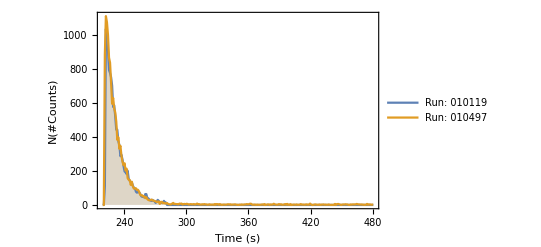

6594

```mathematica
histdata2=HistogramList[data[[Round[dimdata/1.022318];;dimdata,4]]/1000000000,{219,481,1}];
ptdat2=Table[{0,0},{k,1,Dimensions[histdata2[[2]]][[1]]}];
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat2[[i]][[1]]=(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2));
ptdat2[[i]][[2]]=2*histdata2[[2]][[i]];
];
ListLinePlot[{ptdat4,ptdat2},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"Time (s)","N(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLegends->{"Run: 010119","Run: 010497"},Filling->Axis,ImageSize->{1000}]
Total[histdata2[[2]]]
```

```mathematica
Clear[histdata,histdata2]
```

```mathematica
ptdat[[1;;2]]
```

{{75,1},{85,0}}